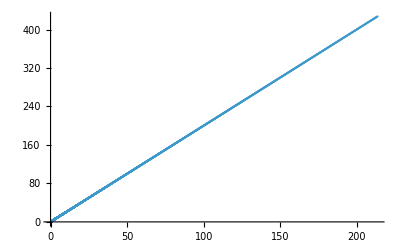

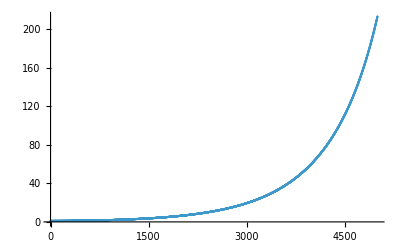

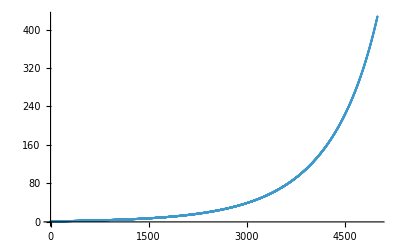

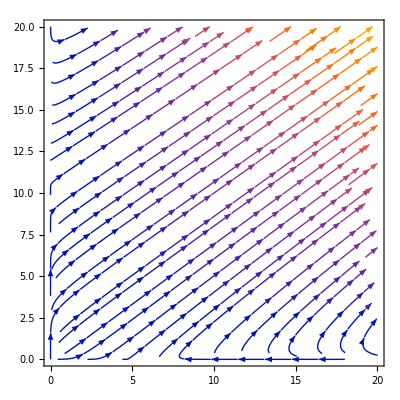

```mathematica
(* СИМБИОЗ ++ *)

NN = 5000;
xyList = Table[0, {i, 0, NN}, {j, 1, 2}];
xList = Table[0, {i, 0, NN}];
yList = Table[0, {i, 0, NN}];

dt = 0.01;
t = 0;
TT = NN dt;
i = 1;

a1 = 0.1; b12 = 0.1;  c1 = 0.2;
a2 = 0.12; b21 = 0.2; c2 = 0.1;

xx0 = 1; yy0 = 1;

While[(t < TT), 
 xx0 += (a1 xx0 + b12 xx0 yy0 - c1 xx0 xx0) dt; 
 yy0 += (a2 yy0 + b21 yy0 xx0- c2 yy0 yy0) dt;
 xyList[[i, 1]] = xx0; xList[[i]] = xx0;
 xyList[[i, 2]] = yy0; yList[[i]] = yy0;
 t += dt;
 i += 1;
 ]

ListPlot[xyList]
ListPlot[xList]
ListPlot[yList]

StreamPlot[{0.1x + 0.3x y -0.02x x, 0.12y + 0.2x y -0.01y y}, {x,0, 20}, {y, 0, 20}]
```

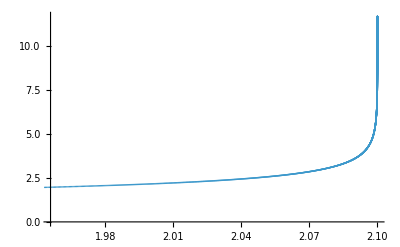

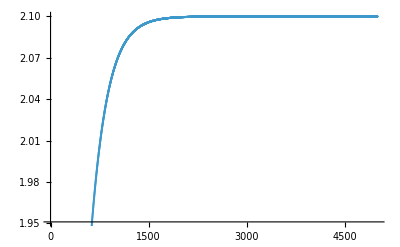

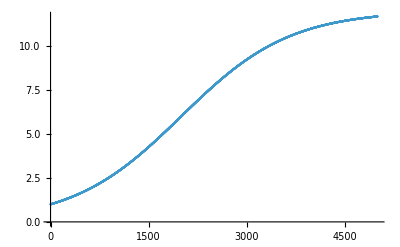

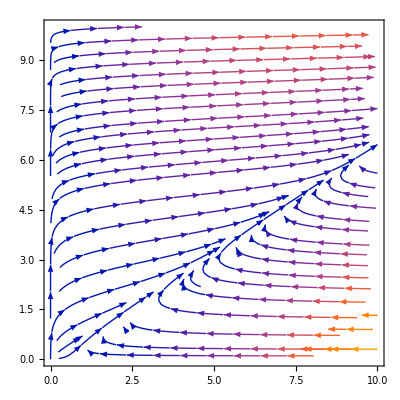

```mathematica
(* КОМЕНСАЛИЗМ +0 *)

NN = 5000;
xyList = Table[0, {i, 0, NN}, {j, 1, 2}];
xList = Table[0, {i, 0, NN}];
yList = Table[0, {i, 0, NN}];

dt = 0.01;
t = 0;
TT = NN dt;
i = 1;



a1 = 0.12; b12 = 0.3;  c1 = 0.2;
a2 = 0.12; b21 = 0; c2 = 0.01;

xx0 = 1; yy0 = 1;

While[(t < TT), 
 xx0 += (a1 xx0 + b12 xx0 yy0 - c1 xx0 xx0) dt; 
 yy0 += (a2 yy0 + b21 xx0 yy0 - c2 yy0 yy0) dt;
 xyList[[i, 1]] = xx0; xList[[i]] = xx0;
 xyList[[i, 2]] = yy0; yList[[i]] = yy0;
 t += dt;
 i += 1;
 ]

ListPlot[xyList]
ListPlot[xList]
ListPlot[yList]

StreamPlot[{0.12x + 0.3x y -0.2x x, 0.12y -0.01y y}, {x,0, 10}, {y, 0, 10}]
```

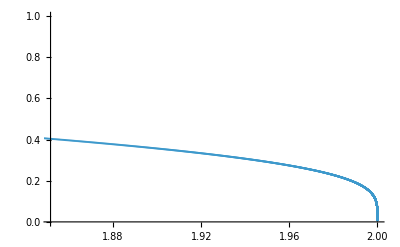

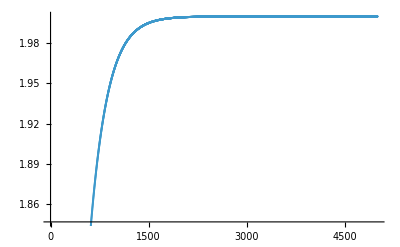

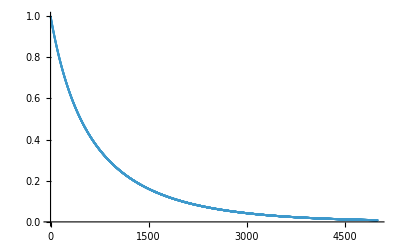

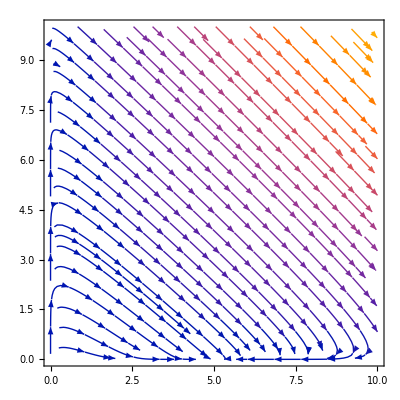

```mathematica
(* ХИЩНИК-ЖЕРТВА +- *)

NN = 5000;
xyList = Table[0, {i, 0, NN}, {j, 1, 2}];
xList = Table[0, {i, 0, NN}];
yList = Table[0, {i, 0, NN}];

dt = 0.01;
t = 0;
TT = NN dt;
i = 1;



a1 = 0.1; b12 = 0.3;  c1 = 0.2;
a2 = 0.12; b21 = -0.2; c2 = 0.1;

xx0 = 1; yy0 = 1;

While[(t < TT), 
 xx0 += (a1 xx0 + b12 xx0 yy0 - c1 xx0 xx0) dt; 
 yy0 += (a2 yy0 + b21 xx0 yy0 - c2 yy0 yy0) dt;
 xyList[[i, 1]] = xx0; xList[[i]] = xx0;
 xyList[[i, 2]] = yy0; yList[[i]] = yy0;
 t += dt;
 i += 1;
 ]

ListPlot[xyList]
ListPlot[xList]
ListPlot[yList]

StreamPlot[{0.1x + 0.3x y -0.02x x, 0.12y -0.3x y -0.01y y}, {x,0, 10}, {y, 0, 10}]
```

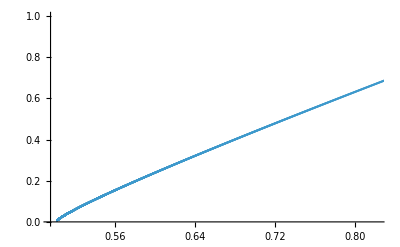

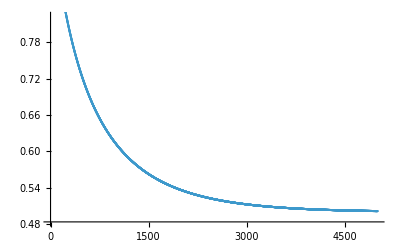

-Graphics-

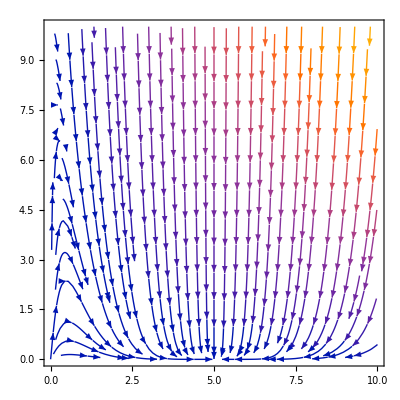

```mathematica
(* АМЕНСАЛИЗМ -0 *) 

NN = 5000;
xyList = Table[0, {i, 0, NN}, {j, 1, 2}];
xList = Table[0, {i, 0, NN}];
yList = Table[0, {i, 0, NN}];

dt = 0.01;
t = 0;
TT = NN dt;
i = 1;



a1 = 0.1; b12 = 0;  c1 = 0.2;
a2 = 0.12; b21 =- 0.2; c2 = 0.1;

xx0 = 1; yy0 = 1;

While[(t < TT), 
 xx0 += (a1 xx0 + b12 xx0 yy0 - c1 xx0 xx0) dt; 
 yy0 += (a2 yy0 + b21 xx0 yy0 - c2 yy0 yy0) dt;
 xyList[[i, 1]] = xx0; xList[[i]] = xx0;
 xyList[[i, 2]] = yy0; yList[[i]] = yy0;
 t += dt;
 i += 1;
 ]

ListPlot[xyList]
ListPlot[xList]
ListPlot[yList]

StreamPlot[{0.1x + 0x y -0.02x x, 0.12y - 0.2x y -0.01y y}, {x,0, 10}, {y, 0, 10}]
```

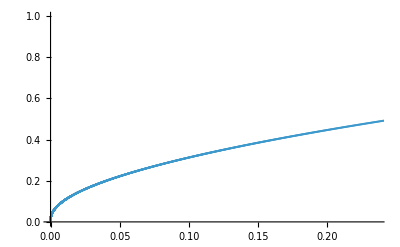

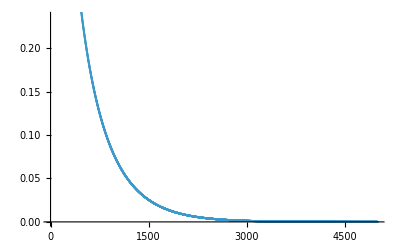

-Graphics-

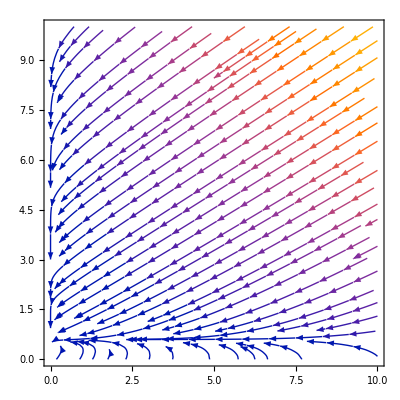

```mathematica
(* КОНКУРЕНЦИЯ -- *)

NN = 5000;
xyList = Table[0, {i, 0, NN}, {j, 1, 2}];
xList = Table[0, {i, 0, NN}];
yList = Table[0, {i, 0, NN}];

dt = 0.01;
t = 0;
TT = NN dt;
i = 1;



a1 = 0.1; b12 = -0.3;  c1 = 0.2;
a2 = 0.12; b21 =- 0.2; c2 = 0.1;

xx0 = 1; yy0 = 1;

While[(t < TT), 
 xx0 += (a1 xx0 + b12 xx0 yy0 - c1 xx0 xx0) dt; 
 yy0 += (a2 yy0 + b21 xx0 yy0 - c2 yy0 yy0) dt;
 xyList[[i, 1]] = xx0; xList[[i]] = xx0;
 xyList[[i, 2]] = yy0; yList[[i]] = yy0;
 t += dt;
 i += 1;
 ]

ListPlot[xyList]
ListPlot[xList]
ListPlot[yList]

StreamPlot[{0.1x -0.3x y -0.02x x, 0.12y - 0.2x y -0.01y y}, {x,0, 10}, {y, 0, 10}]
```

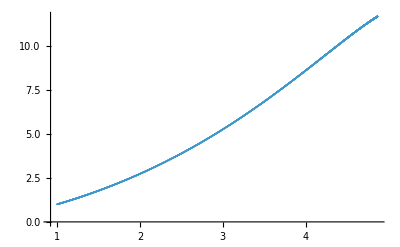

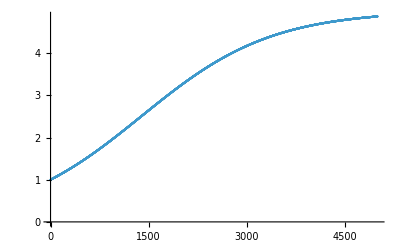

-Graphics-

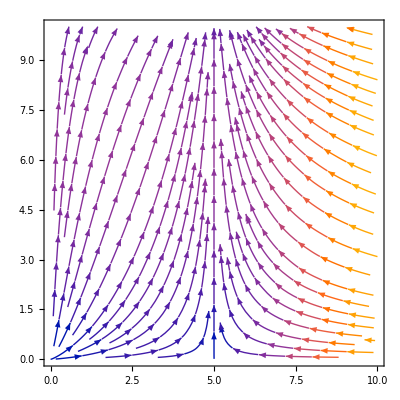

```mathematica
(* НЕЙТРАЛИЗМ 00 *)

NN = 5000;
xyList = Table[0, {i, 0, NN}, {j, 1, 2}];
xList = Table[0, {i, 0, NN}];
yList = Table[0, {i, 0, NN}];

dt = 0.01;
t = 0;
TT = NN dt;
i = 1;



a1 = 0.1; b12 = 0;  c1 = 0.02;
a2 = 0.12; b21 = 0; c2 = 0.01;

xx0 = 1; yy0 = 1;

While[(t < TT), 
 xx0 += (a1 xx0 + b12 xx0 yy0 - c1 xx0 xx0) dt; 
 yy0 += (a2 yy0 + b21 xx0 yy0 - c2 yy0 yy0) dt;
 xyList[[i, 1]] = xx0; xList[[i]] = xx0;
 xyList[[i, 2]] = yy0; yList[[i]] = yy0;
 t += dt;
 i += 1;
 ]

ListPlot[xyList]
ListPlot[xList]
ListPlot[yList]

StreamPlot[{0.1x + 0x y -0.02x x, 0.12y+ 0x y -0.01y y}, {x,0, 10}, {y, 0, 10}]
```